```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
```

```mathematica
(* Parameters *)
t = 1.0;
J=0.4t;
iδ=0.05I;
n=16;
```

```mathematica
greensFunction[k_,ω_]:=1/(ω-J-2t^2/(ω-3J/2))
spectralFunction[k_,ω_]:=-Im[greensFunction[k,ω+iδ]]/Pi/2.
```

```mathematica
spclim=Table[spectralFunction[k,ω],{k,0,2Pi,2Pi/n},{ω,-3,7,0.005}];
```

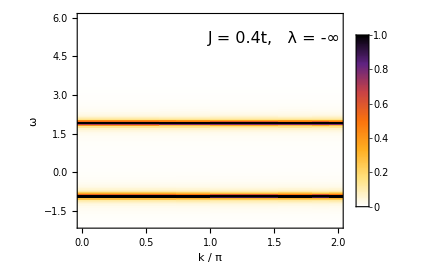

```mathematica
SetOptions[LinTicks,TickLengthScale->1.5];
exactSpc=ListDensityPlot[Transpose[spclim],Frame->True,Axes->False,
FrameStyle->Directive[Black,20,FontFamily->"Bookman Old Style"],
LabelStyle->Directive[Black,12],
DataRange->{{0-1/n,2+1/n},{-3,7}},ImageSize->Medium,
InterpolationOrder->0,
ColorFunction->ColorData[{"SunsetColors","Reverse"}],
PlotRange->{{0,2},{-2,6},{0,1}},
PlotLegends->Placed[Automatic,Right],
ClippingStyle->Automatic,
AspectRatio->.75,
FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks,StripTickLabels[LinTicks]}},
FrameLabel->{"k / π","ω"},
Epilog->Text[
Style[StringJoin["J = ",ToString[NumberForm[J,{3,1}]],"t,   λ = -∞"],Black,16,FontFamily->"Bookman Old Style"],
{1.5,5.2}]
]
```

```mathematica
(*Export["plots/exact/exactLimit.png",exactSpc,ImageResolution->300]*)
```

plots/exact/exactLimit.png